```mathematica
a=Import["~/fw-517-2025-02-27/ACS_LOG_2025-02-26_H12_M22_S01.csv","CSV"];
```

```mathematica
a[[Length[a]]]
```

{2025 Feb 27 13:08:39.811,89198.3,200094.,23.625,0.,0.,21.875,21.375,-13.8125,0.5,21.875,-3.3125,-1.,1}

```mathematica
Length[a[[1]]]
```

14

```mathematica
a[[Length[a]]]
```

{2025 Feb 27 13:08:39.811,89198.3,200094.,23.625,0.,0.,21.875,21.375,-13.8125,0.5,21.875,-3.3125,-1.,1}

```mathematica
b=Transpose[a];
```

```mathematica
c1=Table[{b[[2,i]],b[[9,i]]},{i,Length[b[[2]]]}];
```

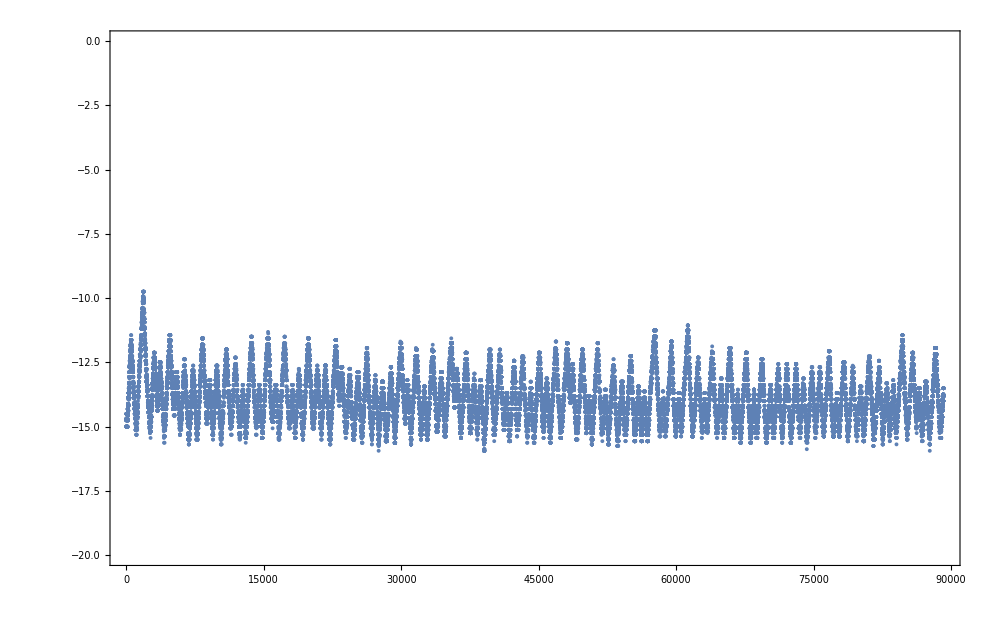

```mathematica
g1=ListPlot[c1,ImageSize->1000,PlotRange->{-20,0},Axes->False,Frame->True]
```

```mathematica
c2=Table[{b[[2,i]],b[[10,i]]},{i,Length[b[[2]]]}];
```

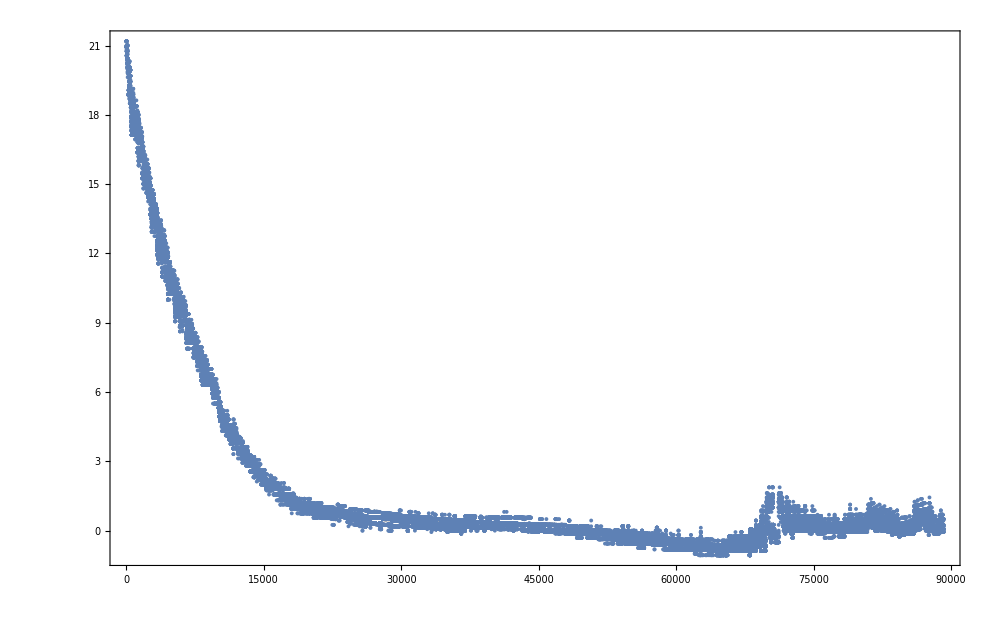

```mathematica
g2=ListPlot[c2,ImageSize->1000,PlotRange->All,Axes->False,Frame->True]
```

```mathematica
c4=Table[{b[[2,i]],b[[12,i]]},{i,Length[b[[2]]]}];
```

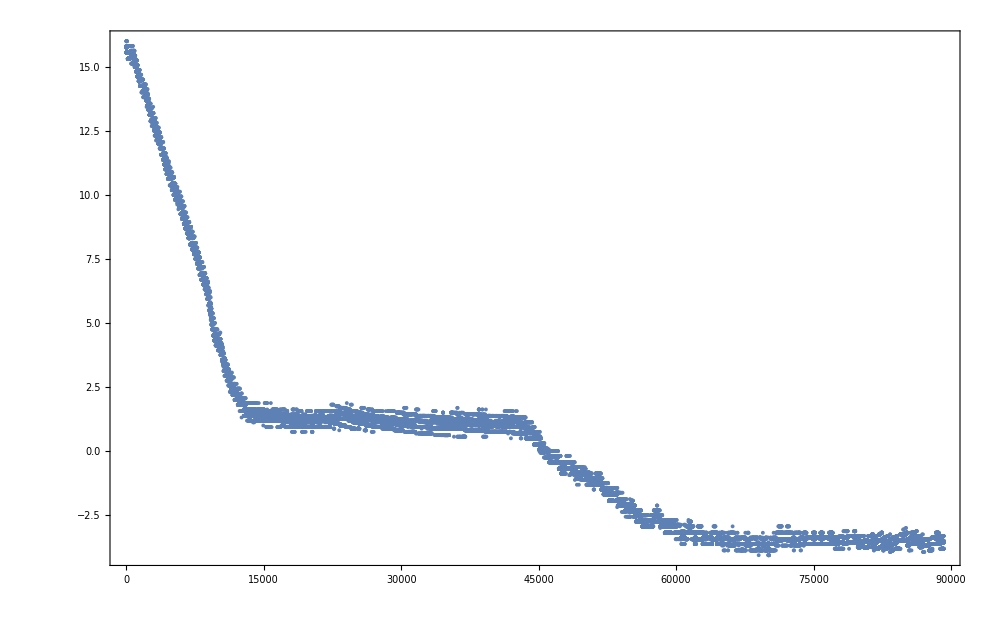

```mathematica
g4=ListPlot[c4,ImageSize->1000,PlotRange->All,Axes->False,Frame->True]
```

```mathematica
c5=Table[{b[[2,i]],b[[13,i]]},{i,Length[b[[2]]]}];
```

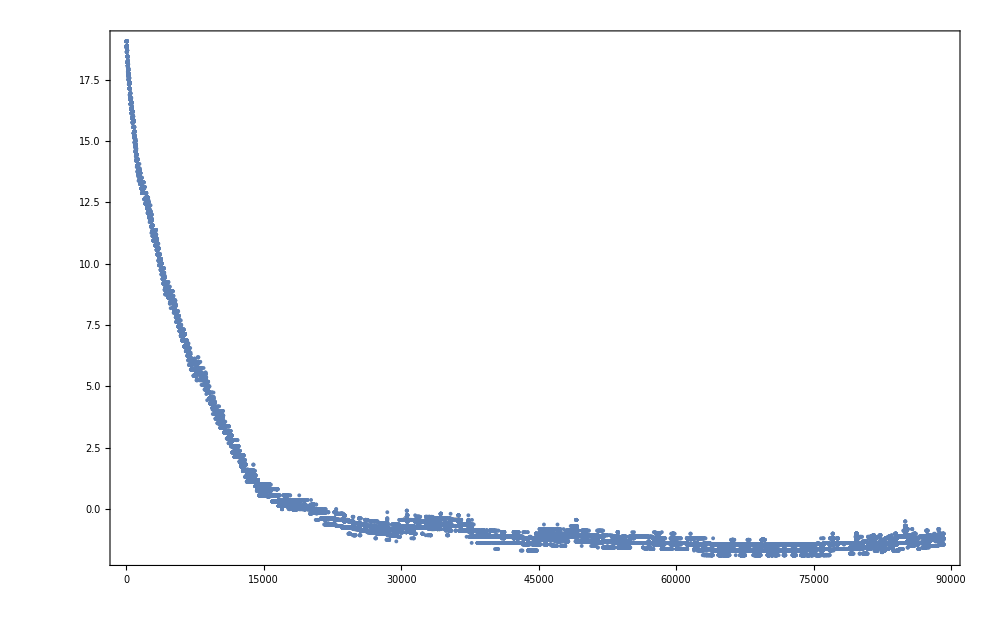

```mathematica
g5=ListPlot[c5,ImageSize->1000,PlotRange->All,Axes->False,Frame->True]
```